-Graphics-

# Quantum interference

## Attenuators in both the arms of Mach-Zehnder

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,ⅈ r},{ⅈ r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2,cc2};
{cb1,cd0}=B[𝓇,𝓉].{cb2,cd1};
```

#### Phase shift in lower path

```mathematica
cd1=ⅇ^(ⅈ ϕ)cd2;
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

```mathematica
ProbabilityOfHeralding[𝓇_,ξ_] = Module[{OperatorCoefficients,ProbTable},
𝓉=√(1-𝓇^2);
OperatorCoefficients =CoefficientList[
S2[ca,cb]
,{ca,cb,cc2,cd1}];

ProbTable=Table[
Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)OperatorCoefficients[[i,j,k,l]]]^2
,{i,1,Dimensions[OperatorCoefficients][[1]]},{j,1,Dimensions[OperatorCoefficients][[2]]},{k,1,Dimensions[OperatorCoefficients][[3]]},{l,1,Dimensions[OperatorCoefficients][[4]]}];
Total[ProbTable[[1,1]],2]
];
ProbabilityOfHeralding[√0.5,0.5]
```

0.830803

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1) - Single-Photon Coincidence

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k  (ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[S2,n,ξ]
n=10;(*total photons max = 2n*)
Prob[n_,ξ_]=(1/Cosh[ξ])^2(1-(Tanh[ξ])^(2(n+1)))/(1-(Tanh[ξ])^2);
S2[ca2_,cb2_]=1/(√Prob[n,ξ])1/Cosh[ξ] Sum[(-Tanh[ξ]ca0 cb0)^k/k!,{k,0,n}];
```

```mathematica
(* Approximation of taking only a few terms 1/(√Prob[n,ξ]) is to renormalize after keeping only first n=nlim terms of the sum*)
```

```mathematica
ClearAll[a,b,c,d,ξ,WithoutHeralding,WithHeralding]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)

ProbabilityWithoutHeralding[ϕ_,𝓇_,ξ_] = Module[{OperatorCoefficients,ProbTable},
𝓉=√(1-𝓇^2);
OperatorCoefficients =√(c!d!)CoefficientList[
CoefficientList[
S2[ca,cb]
,{cc3,cd3}][[c+1,d+1]]
,{ca,cb}];

ProbTable=Table[
Abs[√((i-1)!   (j-1)!)OperatorCoefficients[[i,j]]]^2
,{i,1,Dimensions[OperatorCoefficients][[1]]},{j,1,Dimensions[OperatorCoefficients][[2]]}];
Total[ProbTable,2]
];

ProbabilityWithHeralding[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[
√(c!d! a!b!)CoefficientList[
CoefficientList[
S2[ca,cb]
,{cc3,cd3}][[c+1,d+1]]
,{ca,cb}][[a+1,b+1]]
]^2(*Single number output*)
];
```

```mathematica
(* Visibility *)
VisibilityWithoutHeralding[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=ProbabilityWithoutHeralding [0,𝓇,ξ];
Imin =ProbabilityWithoutHeralding[Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];

VisibilityWithHeralding[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=ProbabilityWithHeralding [0,𝓇,ξ];
Imin =ProbabilityWithHeralding [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

ϕTMSV = 0

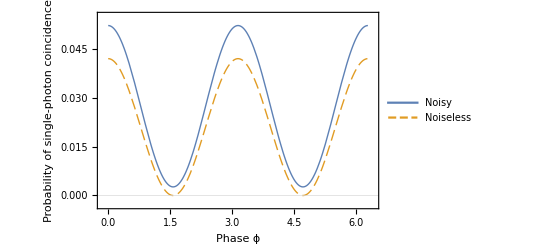

```mathematica
Plot[{ProbabilityWithoutHeralding[ϕ,√0.5,0.5],ProbabilityWithHeralding[ϕ,√0.5,0.5]},{ϕ,0,2π},PlotRange->{0,Full},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},GridLines->{None,{0}},FrameLabel->{"Phase ϕ","Probability of single-photon coincidence","Interference "},LabelStyle-> {Black,Large},PlotLegends->Placed[{"Noisy","Noiseless"},{0.75,0.8}],LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.65],PlotStyle->{Thick,{Thick,Dashing[{0.02,0.009}]}},GridLinesStyle->{Thick,Black},FrameStyle->Thick]
```

```mathematica
{VisibilityWithHeralding[√0.5,0.5],VisibilityWithoutHeralding[√0.5,0.5]}
```

{1.,0.903525}

```mathematica
{imax,imin}={ProbabilityWithoutHeralding [0,√0.5,0.5],ProbabilityWithoutHeralding [π/2,√0.5,0.5]}
```

{0.0521419,0.00264267}

```mathematica
(imax-imin)/(imax+imin)
```

0.903525

```mathematica
(0.05214-0.00264)/(0.05214+0.00264)
```

0.903614

ϕTMSV = π/2

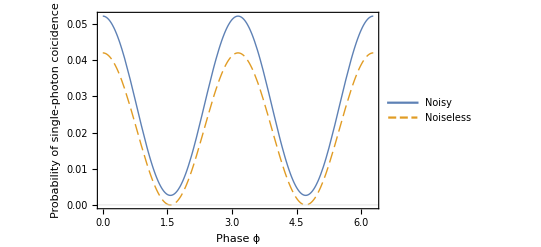

```mathematica
Plot[{wopostselect2[ϕ,√0.5,0.5],wpostselect2[ϕ,√0.5,0.5]},{ϕ,0,2π},PlotRange->{0,Full},Frame->True,GridLines->{None,{0}},FrameLabel->{"Phase ϕ","Probability of single-photon coicidence","Interference "},LabelStyle-> {Black,Large},PlotLegends->Placed[{"Noisy","Noiseless"},{0.75,0.8}],LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.65],PlotStyle->{Thick,{Thick,Dashing[{0.02,0.009}]}},GridLinesStyle->{Thick,Black},FrameStyle->Thick]
```

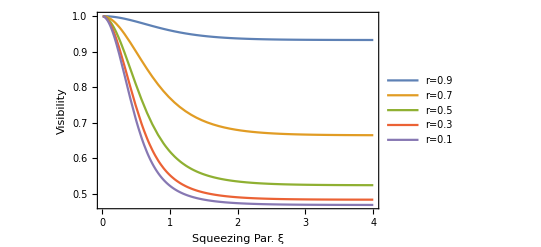

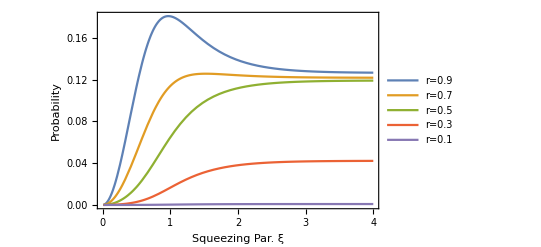

```mathematica
Plot[{Vwo2[0.9,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.32,ξ],Vwo2[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.9,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.30]]
```

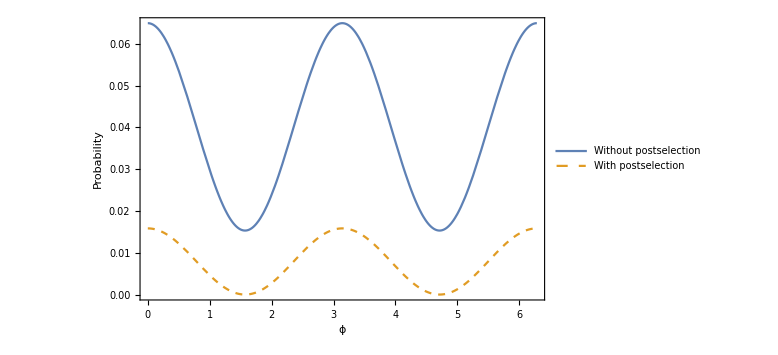

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## Attenuators in both the arms of Mach-Zehnder (inefficient detectors) (modified from “NA v-13.nb”)

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,ⅈ r},{ⅈ r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2p,cc2};
{cb1,cd0}=B[𝓇,𝓉].{cb2p,cd1};
```

#### Fifth and Sixth beam splitters (to simulate inefficient detectors in modes a and b)

```mathematica
{ca2p,cadumpp}=B[𝓇loss,𝓉loss].{ca2,cadump};
{cb2p,cbdumpp}=B[𝓇loss,𝓉loss].{cb2,cbdump};
```

#### Phase shift in lower path

```mathematica
cd1=ⅇ^(-ⅈ ϕ)cd2;
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

```mathematica
(*𝓇loss=√0.9;√(0.10/2);10% total loss of photons in both detectors, due to inefficiency *)
𝓉loss=√(1-𝓇loss^2);
```

## Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb2_,𝓇loss_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)

wopostselect2[ϕ_,𝓇_,ξ_,𝓇loss_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[out2[ca,cb,𝓇loss],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1]];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect2[ϕ_,𝓇_,ξ_,𝓇loss_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out2[ca,cb,𝓇loss],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];

(* Visibility *)
Vwo2[𝓇_,ξ_,𝓇loss_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ,𝓇loss];
Imin =wopostselect2 [Pi/2,𝓇,ξ,𝓇loss];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_,𝓇loss_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ,𝓇loss];
Imin =wpostselect2 [Pi/2,𝓇,ξ,𝓇loss];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

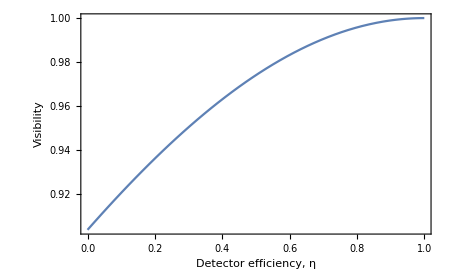

```mathematica
ClearAll[𝓇,ξ]
Plot[{Vw2[√0.5,0.5,√(1-η)]},{η,0,1},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Detector efficiency, η","Visibility","After heralding"},LabelStyle->{Large,Black},ImageSize->Scaled[0.25]]
```

# Quantum states

## Squeezed states through Noiseless Attenuation

## Original

```mathematica
ClearAll[matsq,ξ,k,x]
ψsq[ξ_,nlim_,x_]=1/(√Cosh[ξ])∑_(k=0)^nlim √Binomial[2k,k](-Tanh[ξ]/2)^k(ⅇ^(-x^2/2)/(π^(1/4)√((2k)!2^(2k))))HermiteH[2k,x];(*ca0^(2k)/(√((2k)!));*)
nlim=10;
Wsq[ξ_,nlim_,x_,p_]:=(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψsq[ξ,nlim,x-y/2])] ψsq[ξ,nlim,x+y/2],{y,-10,10}];
limits=3;
range=10;
s=3;
ξ=1/2 Log[s];
Monitor[
matsq=Table[Re[Chop[Wsq[ξ,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
```

```mathematica
Dimensions[matsq]
```

{21,21}

#### s = 3

```mathematica
ListPlot3D[matsq,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.275]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

Model Fitting

```mathematica
ClearAll[a,s,p,x]
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[matsq][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matsq[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,1/π},{σ,1/(√2)},{s,1}},{p,x}]
```

{a→0.31831,σ→0.707107,s→3.}

## After beam splitter

```mathematica
ClearAll[s,ξ,r,t,ca,cb,nlim]
B[r_,t_]={{t,ⅈ r},{ⅈ r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψin[ξ_,nlim_]=Expand[1/(√Cosh[ξ])∑_(k=0)^nlim √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!))];
b=0;(* Post selection *)
s=3;
ξ=1/2 Log[s];
nlim=10;
coefftable=CoefficientList[ψin[ξ,nlim],{cb,ca}];
Pr=Chop[Table[Abs[√((i-1)!   (j-1)!)coefftable[[i,j]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}]];
Dimensions[coefftable]
```

{21,21}

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
Total[Pr,{2}][[0+1]]
```

0.894427

```mathematica
Psucc =∑_(k=0)^20 Abs[(√Binomial[2k,k])/(√Cosh[1/2 Log[3]])(-Tanh[1/2 Log[3]]/2)^k]^2(√0.5)^(2(2k))
```

0.894427

### w/ post selection

```mathematica
ψoutwps[x_]=FullSimplify[Total[Table[√(b!(i-1)!)coefftable[[b+1,i]]ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}]]];
```

#### results

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
Wwps[x_,p_]:=(1/(Total[Pr,{2}][[b+1]]2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y])] ψoutwps[x+(1/2)y],{y,-10,10}];
limits=3;
range=10;
Monitor[
wpsmat=Table[Re[Chop[Wwps[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
Total[wpsmat,2](limits/range)^2
```

0.999472

𝓇=√0.5

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.275]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

#### Fit

𝓇=√0.5

```mathematica
ClearAll[a,σ,s,p,x]
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[wpsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wpsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,1/π},{σ,1/(√2)},{s,1}},{p,x}]
```

{a→0.31831,σ→0.707107,s→1.66667}

### w/o post selection

```mathematica
ψoutwops[x_]=Total[Table[√((i-1)!(j-1)!)coefftable[[i,j]]ψn[j-1,x],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}],{2}];

𝓇=√0.5;
𝓉=√(1-𝓇^2);
(*Wwops[x_,p_]:=Total[Table[(Total[Pr,{2}][[i]]/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwops[x-(1/2)y][[i]])^*ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];*)
Wwops[x_,p_]:=Total[Table[1/(2π)NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwops[x-(1/2)y][[i]])] ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];
limits=3;
range=10;
Monitor[
wopsmat=Table[Re[Chop[Wwops[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
Total[wopsmat,2](limits/range)^2
```

0.998432

𝓇=√0.5

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.275]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

#### Fit

𝓇=√0.5

```mathematica
ClearAll[a,σ,s,p,x]
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[wopsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wopsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,1/π},{σ,1/(√2)},{s,1}},{p,x}]
```

{a→0.275664,σ→0.759836,s→1.73205}

```mathematica
{√(1/(π a/.fit)),(√2 σ/.fit)^1}
```

{1.07457,1.07457}

## Cat States through noiseless attenuation

### Calculation of the Wigner function using number states (and approx. by taking few terms) before Noiseless Attenuation

```mathematica
Psucc[α_,nlim_,t_]=∑_(n=0)^nlim Abs[((( α)^n+( -α)^n)/(√(4 Cosh[Abs[α]^2])√(n!)))]^2 t^(2n);(* Success Probability using formula *)
```

$Aborted

```mathematica
Simplify[∑_(n=0)^20 Abs[((( 2)^n+( -2)^n)/(√(4 Cosh[Abs[2]^2])√(n!)))]^2(√0.5)^(2n),𝓉∈Reals]
```

0.137768

```mathematica
(( 2)^1+( -2)^1)/(√(4 Cosh[Abs[2]^2])√(1!))
```

0

```mathematica
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψc[α_,nlim_,x_]=ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim (α^n (ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x] )/(√n!);
ψcExact[α_,nlim_,x_]=(1/π^(1/4))ⅇ^((-(x-√2 α)^2)/2);(*checked*)
ψCat[α_,nlim_,x_]=(ψc[α,nlim,x]+ψc[-α,nlim,x])/(√(2(1+ⅇ^(-2 Abs[α]^2))));

nlim=20;
WCat[α_,nlim_,x_,p_]:=(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψCat[α,nlim,x-y/2])] ψCat[α,nlim,x+y/2],{y,-10,10}];
WCatExact[α_,nlim_,x_,p_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
```

```mathematica
limits=5;
range=10;
α=2;
matCatExact2=Table[Re[Chop[WCatExact[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
```

```mathematica
Monitor[
matCat=Table[Re[Chop[WCat[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}]
```

$Aborted

```mathematica
NIntegrate[WCat[2,0,x,p],{x,-5,5},{p,-5,5}]
```

0.998934

```mathematica
ListPlot3D[matCatExact2,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W-0.155]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

```mathematica
N[Total[Total[matCatExact2]]](limits/range)^2
```

0.99977

### Calculation of the Wigner function using number states (and approx. by taking few terms) after Noiseless Attenuation

```mathematica
{{|Subscript[ψ, cat]⟩=1/(√(cosh(|α|)^2))∑_(Subscript[n, a]=0)^∞ ∑_(Subscript[n, b]=0)^∞ f(Subscript[n, a],Subscript[n, b])}, {×((tα)^Subscript[n, a](irα)^Subscript[n, b])/(√(Subscript[n, a]!Subscript[n, b]!))|Subscript[n, a]⟩|Subscript[n, b]⟩,}}
```

```mathematica
ψin[α_,nlim_]=Expand[1/(√Cosh[Abs[α]^2])∑_(na=0)^nlim ∑_(nb=0)^nlim (Mod[na+nb+1,2]((𝓉 α)^na(ⅈ 𝓇 α)^nb ca^na cb^nb)/((na!) (nb!)))];
α=2;
nlim=20;

coefftable=CoefficientList[ψin[α,nlim],{cb,ca}];

ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];

OptoN = Table[√((i-1)!(j-1)!),{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}];
Pr=Chop[(OptoN coefftable)*  (OptoN coefftable)];
(*Pr=Chop[Table[Abs[√((i-1)!   (j-1)!)coefftable[[i,j]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}]];*)
Dimensions[coefftable]
NumberStates[x_]=Table[ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}];
b=0;
```

{21,21}

```mathematica
ψin[α,nlim]
```

```mathematica
Simplify[Cosh[4]Total[Pr[[1]]],𝓉∈Reals]//MatrixForm
```

1+8 𝓉^4+(32 𝓉^8)/3+(256 𝓉^12)/45+(512 𝓉^16)/315+(4096 𝓉^20)/14175+(16384 𝓉^24)/467775+(131072 𝓉^28)/42567525+(131072 𝓉^32)/638512875+(1048576 𝓉^36)/97692469875+(4194304 𝓉^40)/9280784638125

```mathematica
Simplify[Cosh[4]Total[Pr,{2}][[0+1]],𝓉∈Reals]
```

1+8 𝓉^4+(32 𝓉^8)/3+(256 𝓉^12)/45+(512 𝓉^16)/315+(4096 𝓉^20)/14175+(16384 𝓉^24)/467775+(131072 𝓉^28)/42567525+(131072 𝓉^32)/638512875+(1048576 𝓉^36)/97692469875+(4194304 𝓉^40)/9280784638125

```mathematica
(*B[r_,t_]={{t,ⅈ r},{ⅈ r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψin[α_,nlim_]=Expand[1/(√(2((1+ⅇ^(-2 Abs[α]^2)))))(ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim ((α^n +(-α)^n)ca0^n )/n!)];
b=0;(* Post selection *)
α=2;
nlim=20;
coefftable=CoefficientList[ψin[α,nlim],{cb,ca}];
OptoN = Table[√((i-1)!(j-1)!),{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}];
Pr=Chop[(OptoN coefftable)*  (OptoN coefftable)];
(*Pr=Chop[Table[Abs[√((i-1)!   (j-1)!)coefftable[[i,j]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}]];*)
Dimensions[coefftable]
NumberStates[x_]=Table[ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}];*)
```

{21,21}

```mathematica
𝓉=√0.5;
Total[Pr,{2}][[0+1]]
```

0.137768

### w/ post selection

```mathematica
ψoutwps[x_]=FullSimplify[Total[OptoN[[b+1,All]] coefftable[[b+1,All]] NumberStates[x]]];
```

```mathematica
(*ψoutwps[x_]=FullSimplify[Total[Table[√(b!(i-1)!)coefftable[[b+1,i]]ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}]]];*)
```

#### results

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
Wwps[x_,p_]:=(1/(Total[Pr,{2}][[b+1]]2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y])] ψoutwps[x+(1/2)y],{y,-10,10}];
limits=5;
range=10;
Monitor[
wpsmat=Table[Re[Chop[Wwps[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
Total[wpsmat,2](limits/range)^2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 7.058×10^-16-7.27919×10^-23 ⅈ and 5.16033×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained -1.19404×10^-15-5.08271×10^-21 ⅈ and 4.81036×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.624845}. NIntegrate obtained -1.6465×10^-13-1.01644×10^-20 ⅈ and 3.41075×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.999999

```mathematica
Total[Pr,{2}][[1]]
```

0.137768

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W-0.040]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W-0.040]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0.5

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

### w/o post selection

```mathematica
ψoutwops[x_]=Total[Table[(coefftable OptoN)[[i,j]] NumberStates[x][[j]],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}] ,{2}];
(*Total[ coefftable OptoN  ConstantArray[NumberStates[x],Dimensions[coefftable][[1]]],{2}];*)
(*ψoutwops[x_]=Total[Table[√((i-1)!(j-1)!)coefftable[[i,j]]ψn[j-1,x],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}],{2}];*)
Dimensions[ψoutwops[x]]
```

{21}

#### results

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
(*Wwops[x_,p_]:=Total[Table[(Total[Pr,{2}][[i]]/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwops[x-(1/2)y][[i]])^*ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];*)
Wwops[x_,p_]:=Total[Table[1/(2π)NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwops[x-(1/2)y][[i]])] ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];
```

```mathematica
limits=5;
range=10;
Monitor[
wopsmat=Table[Re[Chop[Wwops[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}],
{p,x}];
Total[wopsmat,2](limits/range)^2
```

0.999999

r = √0.5

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.275]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0.5

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

## Model fitting

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

### Before

```mathematica
ClearAll[A,α]
model=1((ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2))));
range =(Dimensions[matCatExact2][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matCatExact2[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{A,1},{α,2}},{p,x}]
```

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{A→1.,α→2.}

```mathematica
limits=5;
range=10;
α=α/.fit;
matCatExact=Table[Re[Chop[WCatExact[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListPlot3D[matCatExact,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

### After (w/ post selection)

```mathematica
ClearAll[A,α]
model=1((ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2))));
range =(Dimensions[wpsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wpsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{A,1},{α,2}},{p,x}]
WCatExact[α_,nlim_,x_,p_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
limits=5;
range=10;
matCatExact2=Table[Re[Chop[WCatExact[α/.fit,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListPlot3D[matCatExact2,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

{A→1.,α→1.41422}

-Graphics3D-

This tells the cat state is noiseless after post selection

## Effect of inefficient detector in noiseless attenuation

```mathematica
B[r_,t_]={{t,ⅈ r},{ⅈ r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb1};
{cb1,cdump0}=B[𝓇loss,𝓉loss].{cb,cdump};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
(*ψin[α_,n_]=Expand[1/(√Cosh[Abs[α]^2])(∑_(n=0)^nlim ((α^n +(-α)^n)Simplify[ca0^n])/(n!))];*)
ψin[α_,n_]=Expand[ ca0^0/(√3 √(0!))+ca0^1/(√3 √(1!))+ca0^2/(√3 √(2!))];
b=0;(* Post selection *)
α=2;
(* nlim=20;*)
nlim =2;
coefftable=CoefficientList[ψin[α,nlim],{cb,cdump,ca}];
Pr=ComplexExpand[Chop[Table[Abs[coefftable[[i,j,k]] √((i-1)!   (j-1)!(k-1)!)]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]},{k,1,Dimensions[coefftable][[3]]}]]];
Dimensions[coefftable]
```

{3,3,3}

```mathematica
coefftable//MatrixForm
```

((1/(√3)
𝓉/(√3)
𝓉^2/(√6)) | (-(𝓇 𝓇loss)/(√3)
-√(2/3) 𝓇 𝓇loss 𝓉
0) | ((𝓇^2 𝓇loss^2)/(√6)
0
0)
((ⅈ 𝓇 𝓉loss)/(√3)
ⅈ √(2/3) 𝓇 𝓉 𝓉loss
0) | (-ⅈ √(2/3) 𝓇^2 𝓇loss 𝓉loss
0
0) | (0
0
0)
(-(𝓇^2 𝓉loss^2)/(√6)
0
0) | (0
0
0) | (0
0
0))

```mathematica
ComplexExpand[Pr]//MatrixForm
```

((1/3
𝓉^2/3
𝓉^4/3) | ((𝓇^2 𝓇loss^2)/3
2/3 𝓇^2 𝓇loss^2 𝓉^2
0) | ((𝓇^4 𝓇loss^4)/3
0
0)
((𝓇^2 𝓉loss^2)/3
2/3 𝓇^2 𝓉^2 𝓉loss^2
0) | (2/3 𝓇^4 𝓇loss^2 𝓉loss^2
0
0) | (0
0
0)
((𝓇^4 𝓉loss^4)/3
0
0) | (0
0
0) | (0
0
0))

### w/ post selection

```mathematica
Total[Table[coefftable[[b+1,i,j]] A^(j-1)√(b!(i-1)!(j-1)!),{i,1,Dimensions[coefftable][[2]]},{j,1,Dimensions[coefftable][[3]]}],{2}]//MatrixForm
```

(1/(√3)+(A 𝓉)/(√3)+(A^2 𝓉^2)/(√3)
-(𝓇 𝓇loss)/(√3)-√(2/3) A 𝓇 𝓇loss 𝓉
(𝓇^2 𝓇loss^2)/(√3))

```mathematica
ψoutwps[x_]=FullSimplify[Total[Table[coefftable[[b+1,i,j]]ψn[j-1,x] √(b!(i-1)!(j-1)!),{i,1,Dimensions[coefftable][[2]]},{j,1,Dimensions[coefftable][[3]]}],{2}]];
```

```mathematica
ψoutwps[x]//MatrixForm
```

((ⅇ^(-x^2/2) (2+√2 𝓉 (-𝓉+2 x (1+x 𝓉))))/(2 √3 π^(1/4))
-(ⅇ^(-x^2/2) 𝓇 𝓇loss (1+2 x 𝓉))/(√3 π^(1/4))
(ⅇ^(-x^2/2) 𝓇^2 𝓇loss^2)/(√3 π^(1/4)))

#### results

```mathematica
𝓇=√0.5
𝓉=√(1-𝓇^2)
𝓉loss=√0.75
𝓇loss=√(1-𝓉loss^2)
```

0.707107

0.707107

0.866025

0.5

```mathematica
Wwpsp[x_,p_]:=(1/(Total[Pr,{2,3}][[b+1]]))(1/(2π))Total[Table[NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y][[i]])] ψoutwps[x+(1/2)y][[i]],{y,-10,10}],{i,1,Dimensions[coefftable][[2]]}]];
(*Wwpsp[x_,p_]:=∑_(i=1)^(Dimensions[coefftable][[2]]) (1/(Total[Pr,{3}][[b+1,i]]))(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwps[x-(1/2)y][[i]])^*ψoutwps[x+(1/2)y][[i]],{y,-10,10}];*)

limits=5;
range=10;
Monitor[
wpsmatineff=Table[Re[Chop[Wwpsp[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
```

0.707107

0.707107

0.866025

0.5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 2.8232×10^-15-2.91168×10^-22 ⅈ and 2.06413×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 2.41492×10^-15-7.27919×10^-22 ⅈ and 7.79329×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 4.77687×10^-16-5.29396×10^-23 ⅈ and 3.47508×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Total[wpsmatineff,2](limits/range)^2
```

0.999999

r = √0.5, loss = 100%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss = 50%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.175]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss = 25%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.04]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss = 0%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

```mathematica
mt={{{A1α,A1β,A1γ},{A2α,A2β,A2γ},{A3α,A3β,A3γ}},{{B1α,B1β,B1γ},{B2α,B2β,B2γ},{B3α,B3β,B3γ}},{{C1α,C1β,C1γ},{C2α,C2β,C2γ},{C3α,C3β,C3γ}}};
Total[mt,{2,3}]//MatrixForm
mt[[1,3,1]]
```

(A1α+A1β+A1γ+A2α+A2β+A2γ+A3α+A3β+A3γ
B1α+B1β+B1γ+B2α+B2β+B2γ+B3α+B3β+B3γ
C1α+C1β+C1γ+C2α+C2β+C2γ+C3α+C3β+C3γ)

A3α